```mathematica
xeqs = (D[D[x[τ], τ], τ] == D[ϕ[x[τ], 0], x[τ]] (D[t[τ], τ]^2 - D[x[τ], τ]^2 + D[z[τ], τ]^2) )
```

x''[τ]==(t'[τ]^2-x'[τ]^2+z'[τ]^2) ϕ^(1,0)[x[τ],0]

```mathematica
zeqs = (D[D[z[τ], τ], τ] == D[x[τ], τ] D[ϕ[x[τ], 0], x[τ]](2v/c D[t[τ], τ] - D[z[τ], τ]))
```

z''[τ]==x'[τ] ((2 t'[τ])/3-z'[τ]) ϕ^(1,0)[x[τ],0]

```mathematica
teqs = (D[D[t[τ], τ], τ] == 2v/c D[z[τ], τ] D[x[τ], τ] D[ϕ[x[τ], 0], x[τ]])
```

t''[τ]==2/3 x'[τ] z'[τ] ϕ^(1,0)[x[τ],0]

```mathematica
ϕ[x_, y_, τ_] := 4 Pi (G / c^2) ρ/2 R^2 Log[(x^2 + y^2)/ R]
```

```mathematica
D[ϕ[x[t], 0, t], x[t]]
```

(9.31308×10^-27)/x[t]

```mathematica
FullSimplify[{xeqs, zeqs, teqs}]
```

{x''[τ]==(t'[τ]^2-x'[τ]^2+z'[τ]^2) ϕ^(1,0)[x[τ],0],z''[τ]==x'[τ] ((2 t'[τ])/3-z'[τ]) ϕ^(1,0)[x[τ],0],3 t''[τ]==2 x'[τ] z'[τ] ϕ^(1,0)[x[τ],0]}

```mathematica
G = 6.67*10^(-11);
c = 3*10^8;
R = 1;
v = 1*10^8;
ρ = 1;
```

```mathematica
s = NDSolve[{xeqs, zeqs, teqs, t[0] == 0, x[0] == 5 R, z[0] == 0, t'[0] == 1, x'[0] == v, z'[0] == 0}, {x[τ], z[τ], t[τ]}, {τ, 0, 10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at τ == 0..

NDSolve[{x''[τ]==(t'[τ]^2-x'[τ]^2+z'[τ]^2) ϕ^(1,0)[x[τ],0],z''[τ]==x'[τ] ((2 t'[τ])/3-z'[τ]) ϕ^(1,0)[x[τ],0],t''[τ]==2/3 x'[τ] z'[τ] ϕ^(1,0)[x[τ],0],t[0]==0,x[0]==5,z[0]==0,t'[0]==1,x'[0]==100000000,z'[0]==0},{x[τ],z[τ],t[τ]},{τ,0,10}]

```mathematica
Plot[Evaluate[z[τ]/.s],{τ,0,10},PlotRange->All]
```

ReplaceAll::reps: {NDSolve[{x''[τ]==(((«1»)^(«1»)[«1»])^2-Power[«2»]+((«1»)^(«1»)[«1»])^2) ϕ^(1,0)[x[τ],0],z''[τ]==x'[τ] (2/3 («1»)^(«1»)[«1»]-(«1»)^(«1»)[«1»]) ϕ^(1,0)[x[τ],0],t''[τ]==2/3 x'[τ] z'[τ] ϕ^(1,0)[x[τ],0],t[0]==0,x[0]==5,z[0]==0,t'[0]==1,x'[0]==100000000,z'[0]==0},{x[τ],z[τ],t[τ]},{τ,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x''[0.000204286]==(((«1»)^(«1»)[«1»])^2-Power[«2»]+((«1»)^(«1»)[«1»])^2) ϕ^(1,0)[x[0.000204286],0],z''[0.000204286]==x'[0.000204286] (2/3 («1»)^(«1»)[«1»]-(«1»)^(«1»)[«1»]) ϕ^(1,0)[x[0.000204286],0],«5»,x'[0]==100000000,z'[0]==0},{x[0.000204286],z[«22»],t[«22»]},{0.000204286,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{x''[0.000204286]==(((«1»)^(«1»)[«1»])^2-1. Power[«2»]+((«1»)^(«1»)[«1»])^2) ϕ^(1,0)[x[0.000204286],0.],z''[0.000204286]==x'[0.000204286] (0.666667 («1»)^(«1»)[«1»]-1. («1»)^(«1»)[«1»]) ϕ^(1,0)[x[0.000204286],0.],«5»,x'[0.]==1.×10^8,z'[0.]==0.},{«1»},{0.000204286,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

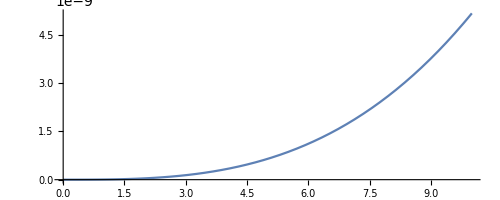

```mathematica
ParametricPlot[Evaluate[{t[τ],z[τ]}/.s],{τ,0,10}]
```